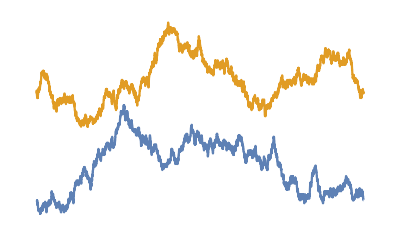
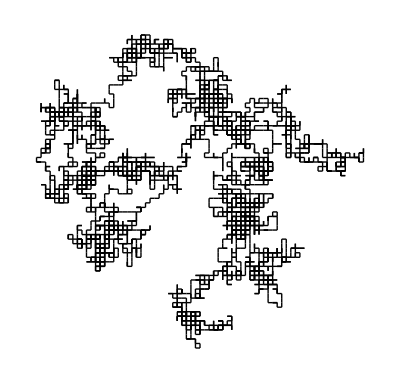

```mathematica
n=5000;
Z=Table[0,{j,1,n+1}];
A=Z;
B=Z;

For[j=1,j<n,++j,A[[j+1]]=A[[j]]+If[2 RandomReal[]>1+A[[j]]/(n-j),1,-1];
B[[j+1]]=B[[j]]+If[2 RandomReal[]>1+B[[j]]/(n-j),1,-1]];

X=n/2+(A+B)/2;
Y=n/2+(A-B)/2;
{ListPlot[{X,n+Sqrt[n]-Y},PlotJoined->True,Axes->False],Graphics[Table[Line[{{X[[j]],Y[[j]]},{X[[j+1]],Y[[j+1]]}}],{j,1,n}]]}
```

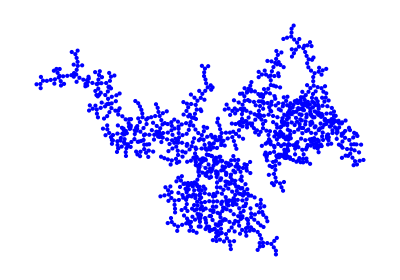
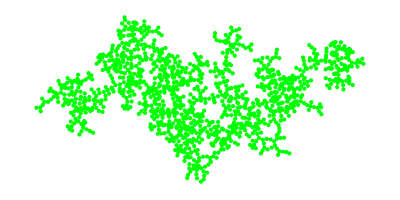

```mathematica
vertnumX=Z+1;
vertnumY=Z+1;
last=Z+1;
minxloc=1;
minyloc=1;

For[j=1,j<n+1,++j,If[X[[j]]<X[[minxloc]],minxloc=j];
If[Y[[j]]<Y[[minyloc]],minyloc=j]];

count=1;

For[j=minxloc,j<n+1,++j,If[X[[j+1]]>X[[j]],vertnumX[[j+1]]=++count;
last[[X[[j+1]]]]=count,vertnumX[[j+1]]=last[[X[[j+1]]]]]];

vertnumX[[1]]=vertnumX[[n+1]];

For[j=1,j<minxloc-1,++j,If[X[[j+1]]>X[[j]],vertnumX[[j+1]]=++count;
last[[X[[j+1]]]]=count,vertnumX[[j+1]]=last[[X[[j+1]]]]]];

vertnumY[[minyloc]]=++count;
last=Z+count;

For[j=minyloc,j<n+1,++j,If[Y[[j+1]]>Y[[j]],vertnumY[[j+1]]=++count;
last[[Y[[j+1]]]]=count,vertnumY[[j+1]]=last[[Y[[j+1]]]]]];

vertnumY[[1]]=vertnumY[[n+1]];

For[j=1,j<minyloc-1,++j,If[Y[[j+1]]>Y[[j]],vertnumY[[j+1]]=++count;
last[[Y[[j+1]]]]=count,vertnumY[[j+1]]=last[[Y[[j+1]]]]]];

{GraphPlot[SimpleGraph[Table[Style[vertnumX[[j]]<->vertnumX[[j+1]],Blue],{j,1,n}]],VertexStyle->Blue,GraphLayout->{"SpringEmbedding"}],GraphPlot[SimpleGraph[Table[Style[vertnumY[[j]]<->vertnumY[[j+1]],Green],{j,1,n}]],VertexStyle->Green,GraphLayout->{"SpringEmbedding"}]}
```

```mathematica
g=Table[0->0,{j,1,3 n/2}];

count=1;

For[j=1,j<=n,++j,g[[count++]]=Style[vertnumX[[j]]<->vertnumY[[j]],Red]];

For[j=1,j<=n,++j,If[X[[j]]<X[[j+1]],g[[count++]]=Style[vertnumX[[j]]<->vertnumX[[j+1]],Blue]]];

For[j=1,j<=n,++j,If[Y[[j]]<Y[[j+1]],g[[count++]]=Style[vertnumY[[j]]<->vertnumY[[j+1]],Green]]];

GraphPlot3D[g,VertexStyle->Table[i->If[i<vertnumY[[minyloc]],Blue,Green],{i,1,n/2+2}],GraphLayout->{"SpringElectricalEmbedding"}]
```

-Graphics3D-

```mathematica
M=SparseArray[Table[0,{j,1,n/2+2},{k,1,n/2+2}]];
For[j=1,j<n+1,j++,M[[vertnumX[[j]],vertnumY[[j]]]]+=1];
x=GraphPlot3D[M,GraphLayout->{"SpringElectricalEmbedding"},VertexShapeFunction->None]
```

-Graphics3D-

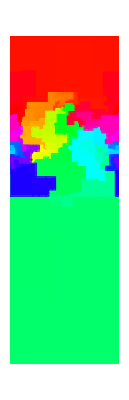
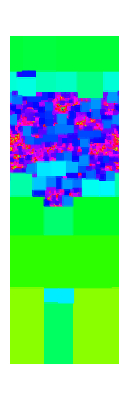

```mathematica
M=M+Transpose[M];
deg=Table[Sum[M[[i,j]],{i,1,n/2+2}],{j,1,n/2+2}];
L=Table[If[i==j,-deg[[i]],M[[i,j]]],{i,1,n/2+2},{j,1,n/2+2}];
a=vertnumX[[minxloc]];
b=vertnumY[[minyloc]];

For[j=1,j<=n/2+2,++j,L[[a,j]]=0;
L[[b,j]]=0;];
L[[a,a]]=1;
L[[b,b]]=1;

v=Table[0,{j,1,n/2+2}];
v[[a]]=1;
w=LinearSolve[N[L],N[v]];

horiz=Table[0,{j,1,n+1}];
vertgap=Table[w[[vertnumY[[j]]]]-w[[vertnumX[[j]]]],{j,1,n+1}];
horiz[[1]]=0;

For[j=1,j<=n,++j,horiz[[j+1]]=horiz[[j]]+vertgap[[j]];];

horizgap=Abs[horiz[[n+1]]];
g=Table[0,{j,1,n}];
count=1;

sq[bot_,top_,left_,hue_]:={Hue[hue],EdgeForm[Thin],Rectangle[{left,bot},{left+(top-bot),top}]};
ssq[bot_,top_,left_,hue_]:={Hue[-Log[Abs[top-bot]+.0000001]/6],EdgeForm[Thin],Rectangle[{left,bot},{left+(top-bot),top}]};

g1=Table[sq[w[[vertnumX[[j]]]],w[[vertnumY[[j]]]],horiz[[j]],j/n],{j,1,n}];
g2=Table[ssq[w[[vertnumX[[j]]]],w[[vertnumY[[j]]]],horiz[[j]],j/n],{j,1,n}];

{Graphics[{g1,Translate[g1,{horizgap,0}],Translate[g1,{2 horizgap,0}]},PlotRange->{{0,horizgap},{0,1}}],Graphics[{g2,Translate[g2,{horizgap,0}],Translate[g2,{2 horizgap,0}]},PlotRange->{{0,horizgap},{0,1}}]}
```

```mathematica
cutoff=.0001;
rvsq[bot_,top_,left_,hue_]:=RevolutionPlot3D[{1,θ},{θ,(2 Pi/horizgap) bot,(2 Pi/horizgap) top+.0000001},{p,(2 Pi/horizgap) left,(2 Pi/horizgap) (left+(top-bot)+.0000001)},Mesh->None,PlotStyle->Hue[hue],BoundaryStyle->{None,Black}];

count=0;
r=Table[0,{j,1,n}];

For[j=1,j<=n,++j,If[Abs[w[[vertnumX[[j]]]]-w[[vertnumY[[j]]]]]>.0001,r[[++count]]=rvsq[w[[vertnumX[[j]]]],w[[vertnumY[[j]]]],horiz[[j]],j/n]];];

Show[Table[r[[j]],{j,1,count}],PlotRange->All,Boxed->False,Axes->False]
```

```mathematica
cutoff=.0001;

spsq[bot_,top_,left_,hue_]:=SphericalPlot3D[1,{p,2 ArcTan[Exp[(2 Pi/horizgap) (bot-1/2)]],2 ArcTan[Exp[(2 Pi/horizgap) (top-1/2)]+.0000001]},{θ,(2 Pi/horizgap) left,(2 Pi/horizgap) (left+(top-bot))+.0000001},Mesh->None,PlotStyle->Hue[hue],BoundaryStyle->{None,Black}];

count=0;
For[j=1,j<=n,++j,If[Abs[w[[vertnumX[[j]]]]-w[[vertnumY[[j]]]]]>.0001,r[[++count]]=spsq[w[[vertnumX[[j]]]],w[[vertnumY[[j]]]],horiz[[j]],j/n]];];

Show[Table[r[[j]],{j,1,count}],PlotRange->All,Boxed->False,Axes->False]
```